### a)

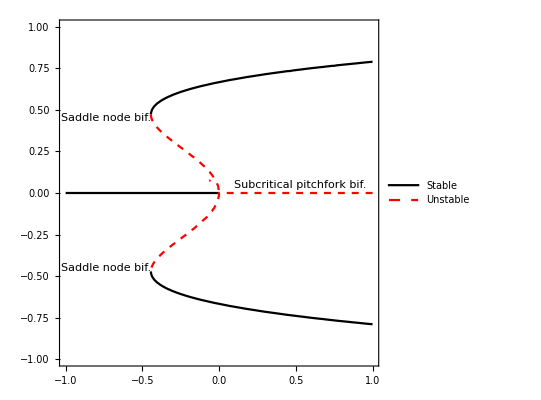

Plot::nonopt: Options expected (instead of {r,-2,2}) beyond position 2 in Plot[f[x],{x,-2,2},{r,-2,2}]. An option must be a rule or a list of rules.

```mathematica
f[x_] := r*x+4*x^3-9*x^5;
dx = D[f[x],x];
cplot = ContourPlot[{
ConditionalExpression[f[x],dx<0]==0,ConditionalExpression[f[x],dx>0]==0},{r,-1,1},{x,-1,1}, ContourStyle->{{Black},{Red,Dashed}},PlotLegends->{"Stable","Unstable"}];
align[Right]={1,0};
align[Center]={0,0};
align[Left]={-1,0};

Text1=Text["Saddle node bif.",{-4/9, 0.45},align[Right]];
Text2=Text["Saddle node bif.",{-4/9,-0.45},align[Right]];
Text3=Text["Subcritical pitchfork bif.",{0.1,0.05},align[Left]];

txt=Graphics[{Text1,Text2,Text3}];
Show[cplot,txt]
```

### b)

```mathematica
Clear[x]
f[x_] := r*x+4*x^3-9*x^5;
dx;
Solve[dx==0,x]
```

{{x→-(√(2-√(4+5 r)))/(√15)},{x→(√(2-√(4+5 r)))/(√15)},{x→-(√(2+√(4+5 r)))/(√15)},{x→(√(2+√(4+5 r)))/(√15)}}

```mathematica
x1 = - Sqrt[2-Sqrt[4+5*r]]/Sqrt[15];
Solve[f[x1]==0,r]
```

-(√(2-√(4+5 r)))/(√15)

```mathematica
{{r->0}}
x2 =  Sqrt[2-Sqrt[4+5*r]]/Sqrt[15];
Solve[f[x2]==0,r]
```

```mathematica
{{r->0}}
x3 = - Sqrt[2+Sqrt[4+5*r]]/Sqrt[15];
Solve[f[x3]==0,r];
```

{{r→0}}

```mathematica
{{r->-4/9}}
x4 = Sqrt[2+Sqrt[4+5*r]]/Sqrt[15];
Solve[f[x4]==0,r]
```

{{r→-4/9}}